# Discrete Variational Symmetrical Top: an Archetype for Rigid-Body Dynamics

Brian Beckman, December 2024

## Abstract

The symmetrical top is a fundamental problem in classical mechanics, an archetype of rigid-body motion. Numerical methods for its solution are likewise an archetype for simulation and control of machines of all kinds: robots, vehicles, conveyances, etc. While an analytical solution for the symmetrical top exists, it is not of interest here. We are interested in numerical methods that generalize to the infinitely more common cases that can on be solved numerically. In fact, we are interested in solution schemas that can be deploy on real-world problems with little up-front tuning, with acceptable error margins, and with good long-term stability.

The discrete method illustrated in this notebook appears to have these properties. While it introduces oscillatory errors in the fourth decimal place, there is no discernable drift. Contrast to the traditional numerical method, which exhibits long-term instability in the conserved quantities of energy and angular momentum. Furthermore, outside of Mathematica, the traditional solution would be difficult to implement and tune, whereas the discrete solution has only one hyperparameter: the time step.

## Introduction

Traditionally, one solves problems in classical mechanics by writing a continuous Lagrangian function, deriving differential equations of motion from its derivatives, and finally discretizing the equations for numerical solution. We call this late discretization. By contrast, with early discretization, one discretizes the Lagrangian itself at the outset. The resulting equations of motion are algebraic, solved by iterated root-finding.

A nagging problem with late discretization is poor conservation of energy and momenta. In practice, numerical solutions of differential equations have long-term drifts. They might need to be periodically corrected or “rebooted.” By contrast, discrete methods, at least theoretically, conserve energy and momenta by construction, thus being stable in the long run.[1, 2, 3]

Numerical methods for differential equations comprise a vast variety of algorithms and sensitive tuning parameters. Bringing a solution to ground can be an expensive process of trial-and-error and compromises. By contrast, discrete methods have only one tuning parameter—the time step.

In this notebook, we contrast a traditional numerical solution for the symmetrical top with a discrete solution. The two solutions match to three significant figures: within the width of a plotting line. The traditional solution exhibits long-term drift in conserved energy and momenta. While small—in the sixth or seventh decimal place—the poor conservation will eventually become noticeable, requiring a “reboot” to keep numerical errors within required limits. By contrast, the discrete solution exhibits only stable oscillatory error in the conserved quantities. While larger—in the fourth or fifth decimal place—these errors are not noticeable, mostly because they do not diverge.

The contribution of this notebook is applying discrete dynamics to this problem from scratch. While we have seen theoretical discrete dynamics for the top,[9] we have not seen a convincing numerical demonstration. Reading the theory leaves us unsatisfied that the method can be effectively, let alone easily, implemented. Here, we show that it can be.

Despite these demonstrable benefits, the discrete implementation in this notebook is too slow. However, with this and our prior successes with discrete harmonic oscillators,[7, 8] we are convinced that the natural benefits of discrete dynamics justify optimizing its implementation.

## References

Marsden and West, 2001, Discrete Mechanics and Variational Integrators, http://www.cds.caltech.edu/~marsden/bib/2001/09-MaWe2001/MaWe2001.pdf

Matthew West, Variational Integrators, Caltech Thesis, May 2004, https://thesis.library.caltech.edu/2492/1/west_thesis.pdf

Marin Kobilarov and Jerrold E. Marsden, Discrete Geometric Optimal Control on Lie Groups, IEEE Transactions on Robotics, Vol. 27, No. 4, August 2011.

https://hepweb.ucsd.edu/ph110b/110b_notes/node36.html

https://bingweb.binghamton.edu/~suzuki/Math-Physics/LN-13S_Symmetric_top.pdf (vetted against Reference 4 in a separate notebook)

William L. Burke, Applied Differential Geometry, Cambridge University Press; 1st edition (January 12, 2008)

Brian C. Beckman, Harmonic Oscillator via Discrete Lagrangian, https://community.wolfram.com/groups/-/m/t/3161109, 2024

Brian C. Beckman, Discrete Damped Harmonic Oscillator, https://community.wolfram.com/groups/-/m/t/3174169, 2024

A. I. Bobenko, Yu. B. Suris, Discrete time Lagrangian mechanics on Lie groups, with an application to the Lagrange top, https://arxiv.org/abs/solv-int/9810018v1, 1998

## Outline

Set up the problem.

Numerically solve the continuous Euler-Lagrange equations, vetting Reference 4.

Explore constants of the motion. Observe numerical drift in energy and momenta.

Formulate and solve the discrete Lagrangian. Compare results with the continuous solution. Observe only stable oscillatory noise.

## Problem Set-Up

There are four parameters or free variables for the problem. Because the top is symmetrical about its spinning axis, its moment-of-inertia tensor has only two independent components, free variables I_1 and I_3. Alternatively, we can model the top as an oblate spheroid with semi-major axis l and equatorial radius s as free variables.

We finesse the issue of consistency between l and I_1. We choose numerical values for them and just ride it out. We might consume inconsistencies into a mass adjustment, but such analysis is uninstructive and unnecessary. We reproduce the continuous solution of Reference 4 without worrying over this issue.

The acceleration of gravity g and the mass m of the top are the other two free variables.

## Continuous Equations of Motion

```mathematica
ClearAll[L,F,V,T,q,ω,ω2,ϕ,θ,ψ,ϕd,θd,ψd,I1,I3, l];
```

### Lagrangian

#### Generalized Coordinates and Velocities

Our generalized coordinates are azimuth ϕ, co-elevation θ, and nodal angle about the spin axis, ψ, i.e., Euler angles in the x-convention (https://mathworld.wolfram.com/EulerAngles.html).

The corresponding generalized velocities are ϕ̇, θ̇, and ψ̇, written as ϕd, θd, ψd because ϕ̇, θ̇, and ψ̇ are not valid Mathematica syntax for variables.

The standard notation ∂L/∂ϕ̇ is a cruel pun. Consider the dedication of Reference 6, “To all those who, like me, have wondered how in hell you can change q̇ without changing q.”

We can’t take the derivative of L with respect to the time derivative ϕ̇=ϕ'[t] of a function ϕ[t]. ∂L/∂ϕ̇ really means ∂L/∂(ϕd), where ϕd is an ordinary parameter variable of the arity-6 Lagrangian function L[ϕ,θ,ψ,ϕd,θd,ψd].

Reference 6 develops the differential-geometry background, from a physicist’s perspective, necessary for the theoretical developments in References 1, 2, 3, and 9. That’s all we have to say about theory in this notebook.

#### Potential Energy

By inspection of the height l of the CG (Center of Gravity) from the contact point:

```mathematica
ClearAll[V];
V[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=m l g Cos[θ];
With[{X={ϕ,θ,ψ,ϕd,θd,ψd}},
V[X]]
```

g l m Cos[θ]

#### Checked

Units of measure: mass * length^2/time^2=energy.

Intuition check: when θ is small, the top is upright and potential energy is high, just like cosine.

The force on the top is

```mathematica
With[{X={ϕ,θ,ψ,ϕd,θd,ψd}},
-D[V[X],θ]]
```

g l m Sin[θ]

acting in the direction of increasing θ, that is, vertically downwards, and larger with larger θ.

#### Kinetic Energy

Consider an inertial reference frame instantaneously oriented with the current Euler angles of the top, but not rotating with the top. Measure the overall angular-velocity vector of the top in this frame in terms of the time derivatives of the angles. Write kinetic energy in terms of that angular-velocity vector in that frame. Denote the 6-tuple {ϕ,θ,ψ,ϕd,θd,ψd} as the state vector X. The [[1,1]] notation in the kinetic-energy formula merely fetches the scalar value from the one-and-only slot in the matrix formula.

```mathematica
ClearAll[M,L,T];
M=({{I1, 0, 0}, {0, I1, 0}, {0, 0, I3}});
ω[{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:={
{ϕd Sin[θ]Sin[ψ]+θd Cos[ψ]},
{ϕd Sin[θ]Cos[ψ]-θd Sin[ψ]},
{ϕd Cos[θ]+ψd}};
T[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=(1/2 ω[X]ᵀ.M.ω[X])[[1,1]];
L[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=T[X]-V[X];
```

#### Checked

Check T against Reference 4 (Mathematica does not automatically reduce T to the right-hand side, and note that === does not work for unknown reasons):

```mathematica
With[{X={ϕ,θ,ψ,ϕd,θd,ψd}},
(T[X]==(1/2 I1(θd^2+Sin[θ]^2 ϕd^2)+1/2 I3(Cos[θ]ϕd+ψd)^2))//FullSimplify]
```

True

Check our L against L hand-copied from Reference 4.

```mathematica
((1/2 I1(ϕd^2 Sin[θ]^2+θd^2)+1/2 I3(ϕd Cos[θ]+ψd)^2-m l g  Cos[θ])
==With[{X={ϕ,θ,ψ,ϕd,θd,ψd}},L[X]])//FullSimplify
```

True

### Euler-Lagrange Equations

Writing ∂L/∂v instead of the pun ∂L/∂q̇, expand

ⅆ/ⅆt(∂L)/(∂v)-(∂L)/(∂q)=0

as v ranges over {ϕd,θd,ψd} and q ranges in lock-step over {ϕ,θ,ψ}.

Here is (∂L)/(∂q) as a column vector. Note the zeros.

```mathematica
ClearAll[dLdq];
(dLdq=(With[{X={ϕ,θ,ψ,ϕd,θd,ψd}},
Table[D[L[X],q],{q,{ϕ,θ,ψ}}]]//FullSimplify))//MatrixForm
```

(0
(g l m-I3 ϕd ψd+(I1-I3) ϕd^2 Cos[θ]) Sin[θ]
0)

See dimensions of energy—mass * length^2/time^2—because ϕ, θ, and ψ, are dimensionless.

Here is (∂L)/(∂v):

```mathematica
ClearAll[dLdqDot];
(dLdqDot=(With[{X={ϕ,θ,ψ,ϕd,θd,ψd}},
Table[D[L[X],qd],{qd,{ϕd,θd,ψd}}]]//FullSimplify))//MatrixForm
```

(I3 ψd Cos[θ]+1/2 ϕd (I1+I3+(-I1+I3) Cos[2 θ])
I1 θd
I3 (ψd+ϕd Cos[θ]))

Now see dimensions of mass * length^2/time rather than mass * length^2/time^2. The second factor of time in the denominator returns via ⅆ/ⅆt.

#### Conjugate Momenta

For any Lagrangian, (∂L)/(∂q̇) (pun intended) are the conjugate momenta p_q. In our case, the first, p_ϕ=(∂L)/(∂ϕ̇), and the third, p_ψ=(∂L)/(∂ψ̇), are conserved momenta, or constants of the motion.(∂L)/(∂ϕ) and (∂L)/(∂ψ) are zero, thus so are ⅆ/ⅆt((∂L)/(∂ϕ̇))=(ⅆ p_ϕ)/ⅆt and ⅆ/ⅆt((∂L)/(∂ψ̇))=(ⅆ p_ψ)/ⅆt by the Euler-Lagrange equations; p_ϕ and p_ψ must be constant because their time derivatives vanish. This is an application of Noether’s Theorem.

Reference 5 exhibits alternative, first-order equations of motion via these constants. We have, in a separate notebook, shown that References 4 and 5 are mutually consistent.

#### Checked

Manually check against Reference 4:

```mathematica
(dLdqDot[[1]]==((I1 Sin[θ]^2+I3 Cos[θ]^2)ϕd+I3 ψd Cos[θ]))//FullSimplify
```

True

```mathematica
(dLdqDot[[3]]==(I3(ψd+ϕd Cos[θ])))
```

True

#### Conjugate Momenta as Functions of State

Define the conjugate momenta as functions of the state X. These will be valuable later for numerical comparisons.

```mathematica
ClearAll[pϕ,pψ];
pϕ[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=((I1 Sin[θ]^2+I3 Cos[θ]^2)ϕd+I3 ψd Cos[θ]);
pψ[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=(I3(ψd+ϕd Cos[θ]));
```

#### Second-Order Equations of Motion

m, I_1, and I_3 are constants. Rewrite their total time derivatives to zero (it’s interesting in some problems to let them vary with time, but not here)

```mathematica
ClearAll[constRules];
constRules={Dt[m,t]->0,Dt[I1,t]->0,Dt[I3,t]->0};
```

Total time derivatives of the conjugate momenta yield second-order terms:

```mathematica
ClearAll[ddLdqDotdt];
(ddLdqDotdt=(Dt[dLdqDot,t]/.constRules//FullSimplify))//MatrixForm
```

(1/2 (I1+I3+(-I1+I3) Cos[2 θ]) Dt[ϕd,t]+I3 Cos[θ] Dt[ψd,t]-(I3 ψd+2 (-I1+I3) ϕd Cos[θ]) Dt[θ,t] Sin[θ]
I1 Dt[θd,t]
I3 (Cos[θ] Dt[ϕd,t]+Dt[ψd,t]-ϕd Dt[θ,t] Sin[θ]))

Finally, the equations of motion, ⅆ/ⅆt(∂L)/(∂q̇)-(∂L)/(∂q)=0:

```mathematica
ClearAll[hardEqns];
(hardEqns=Table[(lhs==0)//FullSimplify,{lhs,ddLdqDotdt-dLdq}])//MatrixForm
```

(1/2 (I1+I3+(-I1+I3) Cos[2 θ]) Dt[ϕd,t]+I3 Cos[θ] Dt[ψd,t]==(I3 ψd+2 (-I1+I3) ϕd Cos[θ]) Dt[θ,t] Sin[θ]
I1 Dt[θd,t]+(-g l m+I3 ϕd ψd+(-I1+I3) ϕd^2 Cos[θ]) Sin[θ]==0
I3 (Cos[θ] Dt[ϕd,t]+Dt[ψd,t])==I3 ϕd Dt[θ,t] Sin[θ])

Set up the equations of motion via symbolic rewrites for numerical solution via NDSolve:

```mathematica
ClearAll[fTimeRules];
fTimeRules={
Dt[ϕd,t]->ϕ''[t],
Dt[θd,t]->θ''[t],
Dt[ψd,t]->ψ''[t],
ϕd->ϕ'[t],
θd->θ'[t],
ψd->ψ'[t],
ϕ->ϕ[t],
θ->θ[t],
ψ->ψ[t]};
```

It’s not easy to interpret, or even believe, these equations straight-up, but the numerical solutions deliver the goods.

```mathematica
(hardEqns/.fTimeRules)//MatrixForm
```

(1/2 (I1+I3+(-I1+I3) Cos[2 θ[t]]) ϕ''[t]+I3 Cos[θ[t]] ψ''[t]==Sin[θ[t]] θ'[t] (2 (-I1+I3) Cos[θ[t]] ϕ'[t]+I3 ψ'[t])
Sin[θ[t]] (-g l m+(-I1+I3) Cos[θ[t]] ϕ'[t]^2+I3 ϕ'[t] ψ'[t])+I1 θ''[t]==0
I3 (Cos[θ[t]] ϕ''[t]+ψ''[t])==I3 Sin[θ[t]] θ'[t] ϕ'[t])

## Numerical Solution

Pick numerical values for the free variables. The “4” reminds us we’re working with Reference 4. In a later notebook, we reconcile these values with Reference 5.

```mathematica
ClearAll[numRules4];
numRules4={g->1,m->1,l->2,I1->2,I3->1};
(hardEqns/.fTimeRules/.numRules4)//MatrixForm
```

(1/2 (3-Cos[2 θ[t]]) ϕ''[t]+Cos[θ[t]] ψ''[t]==Sin[θ[t]] θ'[t] (-2 Cos[θ[t]] ϕ'[t]+ψ'[t])
Sin[θ[t]] (-2-Cos[θ[t]] ϕ'[t]^2+ϕ'[t] ψ'[t])+2 θ''[t]==0
Cos[θ[t]] ϕ''[t]+ψ''[t]==Sin[θ[t]] θ'[t] ϕ'[t])

Change tN if you want a longer integration.

```mathematica
ClearAll[tN];
tN=70;
```

Mathematica has no trouble, numerically, with these equations, given plausible initial conditions. There is a great deal of automation hidden in this call: automatic (and opaque) choice of algorithm, time step, and various tuning parameters. If we were writing an integrator from scratch, we would have much work to show.

```mathematica
ClearAll[nsoln];
nsoln=NDSolve[(hardEqns/.fTimeRules/.numRules4)~Join~{
ϕ[0]==0,ϕ'[0]==0,
θ[0]==42°,θ'[0]==0,
ψ[0]==0,ψ'[0]==5},
{ϕ[t],θ[t],ψ[t]},
{t,0,tN}]
```

{{ϕ[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],ψ[t]→InterpolatingFunction[…][t]}}

### Conservation of Energy

Write the energy E_4[X] as a function of state X. The subscript “4” again reminds us that we’re checking Reference 4.

```mathematica
ClearAll[E4];
E4[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=T[X]+V[X];
```

```mathematica
With[{X={ϕ[t],θ[t],ψ[t],ϕ'[t],θ'[t],ψ'[t]}},
E4[X]]/.numRules4//FullSimplify
```

2 Cos[θ[t]]+θ'[t]^2-1/4 (-3+Cos[2 θ[t]]) ϕ'[t]^2+Cos[θ[t]] ϕ'[t] ψ'[t]+1/2 ψ'[t]^2

#### Funny Plotting Business

We need derivatives of the angles with respect to time to plot energy and momentum. It’s not immediately straightforward to compute derivatives of  NDsolve’s results, which are not functions, but expressions depending on the hard-coded parameter t. Mathematica’s Derivative function requires functions, not expressions.

Convert the expressions to functions. Also, avoid the Symbol t, even if encapsulated in Modules or as dummy variables in Plot. To wit, the following does not work:

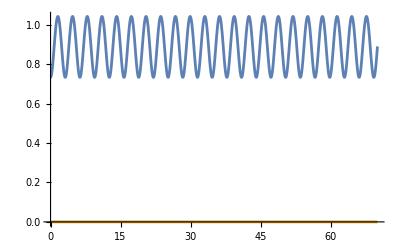

```mathematica
Module[{fθ},
fθ[u_]:=((θ[t]/.nsoln)/.{t->u});
Plot[{fθ[t],fθ'[t]},{t,0,tN}]]
```

The following DOES work, so long as the dummy variable in Plot is anything except t:

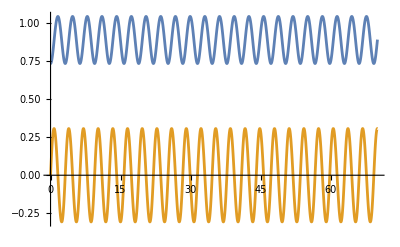

```mathematica
Module[{fθ},
fθ[u_]:=((θ[t]/.nsoln[[1]])/.{t->u});
Plot[{fθ[u],fθ'[u]},{u,0,tN}]]
```

We’re now equipped to compute energy and momenta.

#### Checked

Energy, about 14 Joule, is conserved to five figures. It is, however, trending upwards due to numerical effects, which we will not see in the discrete solution.

13.9863

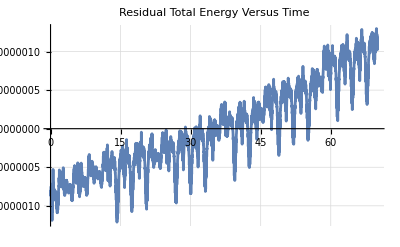

```mathematica
ClearAll[displayResidualEnergy];
displayResidualEnergy[Efunction_,label_]:=
Module[{fϕ,fθ,fψ,X,meanEf},
fϕ[u_]:=((ϕ[t]/.nsoln[[1]])/.{t->u});
fθ[u_]:=((θ[t]/.nsoln[[1]])/.{t->u});
fψ[u_]:=((ψ[t]/.nsoln[[1]])/.{t->u});
X[u_]:={fϕ[u],fθ[u],fψ[u],fϕ'[u],fθ'[u],fψ'[u]};
(* mean Energy of the entire run *);
meanEf=Echo@Mean[Table[(Efunction[X[u]]/.numRules4),{u,0,tN,(tN-0)/100}]];
Plot[(Efunction[X[u]]/.numRules4)-meanEf,{u,0,tN},FrameLabel->{{"Energy [Joule]",""},{"Time [sec]",""}},
PlotLabel->label,Frame->Automatic,GridLines->Automatic]];
displayResidualEnergy[E4,"Residual Total Energy Versus Time"]
```

It turns out that two addends of energy are separately conserved, again with small, pesky drifts. The first and smaller, E_1, is the potential energy plus the kinetic energy of nutation angle θ plus the kinetic energy due to the (smaller) precession component, ϕd sin θ, perpendicular to the instantaneous axis of rotation:

1.48629

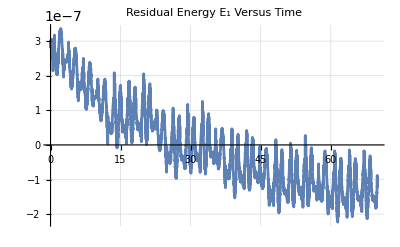

```mathematica
ClearAll[E1];
E1[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=m g l Cos[θ]+1/2 I1(θd^2+ϕd^2 Sin[θ]^2);
displayResidualEnergy[E1,"Residual Energy E_1 Versus Time"]
```

The second and larger conserved energy, E_2, is the kinetic energy of spin plus the kinetic energy due to the (larger) precession component, ϕd cos θ, parallel to the instantaneous axis of rotation:

12.5

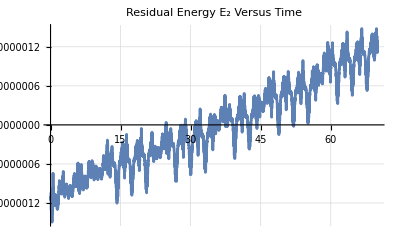

```mathematica
ClearAll[E2];
E2[X:{ϕ_,θ_,ψ_,ϕd_,θd_,ψd_}]:=1/2 I3(ϕd Cos[θ]+ψd)^2;
displayResidualEnergy[E2,"Residual Energy E_2 Versus Time"]
```

### Conservation of Momenta

Check conservation of azimuthal p_ϕ and nodal p_ψ momenta via the functional forms defined above. See conservation within six figures with opposite drifts.

3.71572

5.

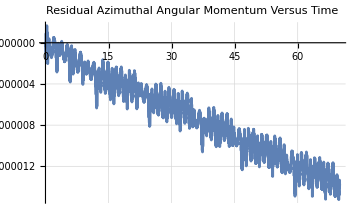
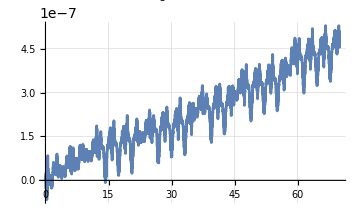

```mathematica
Module[{fϕ,fθ,fψ,X,meanPϕ,meanPψ},
fϕ[u_]:=((ϕ[t]/.nsoln[[1]])/.{t->u});
fθ[u_]:=((θ[t]/.nsoln[[1]])/.{t->u});
fψ[u_]:=((ψ[t]/.nsoln[[1]])/.{t->u});
X[u_]:={fϕ[u],fθ[u],fψ[u],fϕ'[u],fθ'[u],fψ'[u]};
meanPϕ=Echo@Mean[Table[pϕ[X[u]]/.numRules4,{u,0,tN,100}]];
meanPψ=Echo@Mean[Table[pψ[X[u]]/.numRules4,{u,0,tN,100}]];
Row[{
Plot[(pϕ[X[u]]/.numRules4)-meanPϕ,{u,0,tN},ImageSize->Medium,PlotLabel->"Residual Azimuthal Angular Momentum Versus Time",Frame->Automatic,GridLines->Automatic],
Plot[(pψ[X[u]]/.numRules4)-meanPψ,{u,0,tN},ImageSize->Medium,PlotLabel->"Residual Nodal Angular Momentum Versus Time",Frame->Automatic,GridLines->Automatic]}]]
```

### Interactive Exploration

NDSolve is so fast that we can put it in a Manipulate to play around with initial conditions and integration time.

Graphics helpers:

```mathematica
ClearAll[jack,eulerRotate];
With[{o={0,0,0},
e1={1,0,0},e2={0,1,0},e3={0,0,1},
tip={0,0,1},pr=1.25},
eulerRotate[obj_,ϕ_,θ_,ψ_]:=
With[{r3=RotationMatrix[ϕ,e3]},
With[{e1Prime=r3.e1},
With[{e3DoublePrime=
RotationMatrix[θ,e1Prime].r3.e3},
Rotate[
Rotate[
Rotate[
obj,
ϕ,e3],
θ,e1Prime],
ψ,e3DoublePrime]]]];
jack[opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,e1},diameter]]},
{Darker[Green],Arrow[Tube[{o,e2},diameter]]},
{Blue,Arrow[Tube[{o,e3},diameter]]},
{Lighter[Cyan],Arrow[Tube[{o,-e1},diameter]]},
{Magenta,Arrow[Tube[{o,-e2},diameter]]},
{Yellow,Arrow[Tube[{o,-e3},diameter]]}}]
```

A rendering function:

```mathematica
ClearAll[renderSoln];
renderSoln[nsoln_,tn_]:=
With[{pr=1.25,e1={1,0,0},e2={0,1,0},e3={0,0,1},squish=0.0001},
With[{prl={{-pr,pr},{-pr,pr},{-pr,pr}}},
Show[
Graphics3D[{
jack[.25,0.0125],
Opacity[0.1],Sphere[],
Opacity[0.05],
Blue,Cylinder[squish{-e3,e3}],
Red,Cylinder[squish{-e1,e1}],
Green,Cylinder[squish{-e2,e2}]}],
ParametricPlot3D[{
Sin[θ[t]]Cos[ϕ[t]],
Sin[θ[t]]Sin[ϕ[t]],
Cos[θ[t]]}/.nsoln,{t,0,tn},PlotRange->prl,AspectRatio->{1,1,1}]]]];
```

Here is a playground with manipulable initial spin speed ψd, precession throw ϕd, and dip angle θ_0. See the obvious nutation and precession.

Amongst interesting exercises, check that, with no initial spin, the top just falls over, i.e., rotates around the y axis because we don’t have a “hard floor”. This presages the inverted spherical pendulum, the next problem in this series of notebooks on discrete dynamics.

```mathematica
With[{initials={ϕ[0]==0°,θ'[0]==0,ψ[0]==0°},
eqns=(hardEqns/.fTimeRules/.numRules4)},
Manipulate[
Module[{nsoln=NDSolve[
eqns~Join~initials~Join~{
ψ'[0]==ψd0,θ[0]==θ0 °,ϕ'[0]==ϕd0},
{ϕ[t],θ[t],ψ[t]},
{t,0,tn}]},
renderSoln[nsoln,tn]],
{{tn,70,"t_N[sec]"},0,140,Appearance->"Open"},
{{ϕd0,0,"ϕ̇[rad/s]"},0,3,Appearance->"Open"},
{{ψd0,5,"spin[rad/s]"},0,30,Appearance->"Open"},
{{θ0,42,"dip[deg]"},0,90,Appearance->"Open"}]]
```

## Discrete Solution

### Discrete Lagrangian

Recall the Lagrangian from above.

```mathematica
With[{X={ϕ,θ,ψ,ϕd,θd,ψd}},
L[X]//FullSimplify]
```

1/2 (-2 g l m Cos[θ]+I3 (ψd+ϕd Cos[θ])^2+I1 (ϕd Cos[ψ] Sin[θ]-θd Sin[ψ])^2+I1 (θd Cos[ψ]+ϕd Sin[θ] Sin[ψ])^2)

The third, unnumbered equation on page 643 of Reference 3 has a useful definition of the discrete Lagrangian, with h as time step.

It is beautifully simple and easy to memorize, though it has units of action rather than of energy.

```mathematica
ClearAll[Ld];
Ld[ϕl_,θl_,ψl_,ϕr_,θr_,ψr_]:=h L[{(ϕl+ϕr)/2,(θl+θr)/2,(ψl+ψr)/2,(ϕr-ϕl)/h,(θr-θl)/h,(ψr-ψl)/h}];
```

### Discrete Euler-Lagrange Equations

Reference 2 gives us the forced discrete Euler-Lagrange Equations.

We don't need the force terms here. Write out 1.28 from above,  just with k-1,k,k+1 as the triplet of indices instead of k,k+1,k+2.

D_2 L_d(q_(k-1),q_k)+D_1 L_d(q_k,q_(k+1))==0

```mathematica
ClearAll[rl,rr,eqnsdSimp,eqnsd];
rl={ϕl->ϕkm1,θl->θkm1,ψl->ψkm1,ϕr->ϕk,θr->θk,ψr->ψk};
rr={ϕl->ϕk,θl->θk,ψl->ψk,ϕr->ϕkp1,θr->θkp1,ψr->ψkp1};
eqnsdSimp=((
{((D[Ld[ϕl,θl,ψl,ϕr,θr,ψr],ϕr]/.rl)+
(D[Ld[ϕl,θl,ψl,ϕr,θr,ψr],ϕl]/.rr))==0,
((D[Ld[ϕl,θl,ψl,ϕr,θr,ψr],θr]/.rl)+
(D[Ld[ϕl,θl,ψl,ϕr,θr,ψr],θl]/.rr))==0,
((D[Ld[ϕl,θl,ψl,ϕr,θr,ψr],ψr]/.rl)+
 (D[Ld[ϕl,θl,ψl,ϕr,θr,ψr],ψl]/.rr))==0})/.numRules4//FullSimplify);
eqnsd[ha_,ϕkm1a_,θkm1a_,ψkm1a_,ϕka_,θka_,ψka_]:=eqnsdSimp/.{h->ha,ϕkm1->ϕkm1a,θkm1->θkm1a,ψkm1->ψkm1a,ϕk->ϕka,θk->θka,ψk->ψka};
eqnsd[h,ϕkm1,θkm1,ψkm1,ϕk,θk,ψk]
```

{(3 (-2 ϕk+ϕkm1+ϕkp1)+2 (-ψk+ψkm1) Cos[(θk+θkm1)/2]+(ϕk-ϕkm1) Cos[θk+θkm1]+2 (-ψk+ψkp1) Cos[(θk+θkp1)/2]+(ϕk-ϕkp1) Cos[θk+θkp1])/h==0,(16 θk-8 (θkm1+θkp1)+2 (2 h^2-(ϕk-ϕkm1) (ψk-ψkm1)) Sin[(θk+θkm1)/2]+(ϕk-ϕkm1)^2 Sin[θk+θkm1]+2 (2 h^2-(ϕk-ϕkp1) (ψk-ψkp1)) Sin[(θk+θkp1)/2]+(ϕk-ϕkp1)^2 Sin[θk+θkp1])/h==0,(2 ψk-ψkm1-ψkp1+(ϕk-ϕkm1) Cos[(θk+θkm1)/2]+(ϕk-ϕkp1) Cos[(θk+θkp1)/2])/h==0}

### Results and Conclusion

We solve these equations by finding the roots ϕ_(k+1), θ_(k+1), and ψ_(k+1) given values for ϕ_k, θ_k, and ψ_k and ϕ_(k-1), θ_(k-1), and ψ_(k-1), bootstrapped with the first two values from the continuous solution. Notice there are no explicit velocities to deal with. This is a bonus simplification over the continuous method.

The following plot shows angular differences between the continuous and discrete solutions for the first 14 seconds at a time step of 0.01 seconds for the discrete solution. The difference shows a periodic error of amplitude around 0.0025 rad, or about 4.2 arc minutes, and a maximum constant systematic error in the spin angle of around 0.05 rad, or about 1.4 deg. The constant systematic error in the other two angles is much smaller. The systematic error in spin angle is likely due to the bootstrapping procedure and could be mitigated by a more careful initialization of the solution. None of these errors are big enough to be visually discernable in an animation or a line plot of the solutions.

The big-picture point is, however, is that the errors of the discrete solution do not grow or shrink. We know that the continuous solution has long-term drift that, while small, will eventually diverge. This implementation of the discrete solution is too slow to extend it to long durations or short time steps, as may be seen by adjusting h and tn below. While we have good theoretical reasons to believe it is stable, long term,[1, 2, 3] we have not numerically demonstrated that stability here.

The discrete solution does a qualitatively good job with a coarse time step of 0.01 seconds, quite large in the scheme of things, and presumably much larger than the time step Mathematica chooses internally to NDsolve for the continuous solution. The point of this notebook is not speed of implementation, but validation of both implementation ease and stability of conserved quantities. An optimized implementation could likely be made very fast. The chief suspect is root-finding. We might experiment in the future with a hand-crafted Newton-Raphson method.

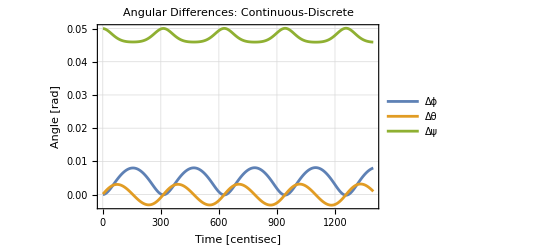

```mathematica
h=1/100;
tn=14;
len=tn/h;
dsoln=ConstantArray[0,{6,len}];
dsoln[[1;;3,1]]=Map[#[[2]]&,nsoln[[1]]/.{t->0}];
dsoln[[1;;3,2]]=Map[#[[2]]&,nsoln[[1]]/.{t->h}];
For[j=2,j<len,j+=1,
Module[{pj=eqnsd[h,dsoln[[1,j-1]],dsoln[[2,j-1]],dsoln[[3,j-1]],dsoln[[1,j]],dsoln[[2,j]],dsoln[[3,j]]],r},
r=FindRoot[pj,MapThread[List,{{ϕkp1,θkp1,ψkp1},{dsoln[[1,j]],dsoln[[2,j]],dsoln[[3,j]]}}]];
dsoln[[1;;3,j+1]]=r[[;;,2]];
dsoln[[4;;6,j+1]]=(dsoln[[1;;3,j+1]]-dsoln[[1;;3,j]])/h;    ]];
fϕ[u_]:=((ϕ[t]/.nsoln)/.{t->u})[[1]];
fθ[u_]:=((θ[t]/.nsoln)/.{t->u})[[1]];
fψ[u_]:=((ψ[t]/.nsoln)/.{t->u})[[1]];
Δϕ=Table[fϕ[u*h]-dsoln[[1,u]],{u,3,len}];
Δθ=Table[fθ[u*h]-dsoln[[2,u]],{u,3,len}];
Δψ=Table[fψ[u*h]-dsoln[[3,u]],{u,3,len}];
ListLinePlot[{Δϕ,Δθ,Δψ},PlotLegends->{"Δϕ","Δθ","Δψ"},PlotLabel->"Angular Differences: Continuous-Discrete",
Frame->True,GridLines->Automatic,FrameLabel->{{"Angle [rad]",""},{"Time [centisec]",""}}]
```

### Conservation of Energy

Examine the energy of the first 14 seconds. Recall that the continuous solution steadily and unrealistically gains energy.

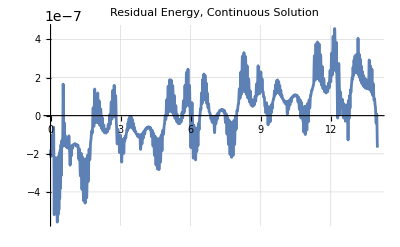

```mathematica
Module[{fϕ,fθ,fψ,X,mean},
fϕ[u_]:=((ϕ[t]/.nsoln[[1]])/.{t->u});
fθ[u_]:=((θ[t]/.nsoln[[1]])/.{t->u});
fψ[u_]:=((ψ[t]/.nsoln[[1]])/.{t->u});
X[u_]:={fϕ[u],fθ[u],fψ[u],fϕ'[u],fθ'[u],fψ'[u]};
mean=Mean[Table[E4[X[u]]/.numRules4,{u,0,14,1}]];
Plot[(E4[X[u]]/.numRules4)-mean,{u,0,14},
PlotLabel->"Residual Energy, Continuous Solution",
Frame->Automatic,GridLines->Automatic,FrameLabel->{{"Residual Energy [Joule]",""},{"Time [sec]",""}}]]
```

The energy error of the discrete solution, while oscillating in the fourth figure, does not drift, despite the coarse time step of 0.01 seconds. In perspective, the initial condition for spin rate is 5 radians per second (~48 RPM), so a hundredth of a second is a little less than a hundredth of a revolution, or around 3 or 4 degrees, maybe just enough time to track precession and nutation. The fact that the discrete solution tracks energy in the mean without drift with such a coarse time step is remarkable, and is one of the great selling points of discrete dynamics.

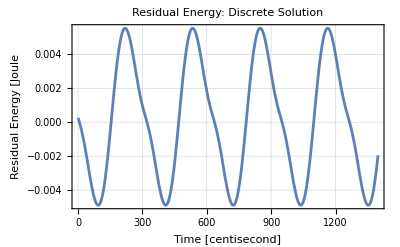

```mathematica
Module[{mean,energy=Table[E4[dsoln[[;;,u]]]/.numRules4,{u,3,len}]},
mean=Mean[energy];
ListLinePlot[Table[(E4[dsoln[[;;,u]]]/.numRules4)-mean,{u,3,len}],
PlotLabel->"Residual Energy: Discrete Solution",
FrameLabel->{{"Residual Energy [Joule",""},{"Time [centisecond]",""}},
Frame->True,GridLines->Automatic]]
```

### Conservation of Momenta

First, compare the drift of the continuously derived azimuthal momentum versus the mere oscillation, albeit much larger, of the error in the discretely derived azimuthal momentum.

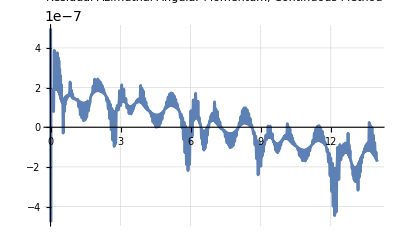

```mathematica
Module[{fϕ,fθ,fψ,X,mean},
fϕ[u_]:=((ϕ[t]/.nsoln[[1]])/.{t->u});
fθ[u_]:=((θ[t]/.nsoln[[1]])/.{t->u});
fψ[u_]:=((ψ[t]/.nsoln[[1]])/.{t->u});
X[u_]:={fϕ[u],fθ[u],fψ[u],fϕ'[u],fθ'[u],fψ'[u]};
mean=Mean[Table[(pϕ[X[u]]/.numRules4),{u,0,14,1}]];
Plot[(pϕ[X[u]]/.numRules4)-mean,{u,0,14},
PlotLabel->"Residual Azimuthal Angular Momentum, Continuous Method",
FrameLabel->{{"Angular Momentum [Joule-sec]",""},{"Time [sec]",""}},
Frame->Automatic,GridLines->Automatic]]
```

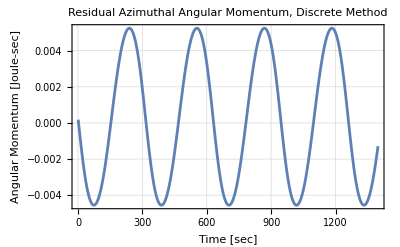

```mathematica
Module[{mean},
mean=Mean[Table[pϕ[dsoln[[;;,u]]]/.numRules4,{u,3,len}]];
ListLinePlot[Table[(pϕ[dsoln[[;;,u]]]/.numRules4)-mean,{u,3,len}],
PlotLabel->"Residual Azimuthal Angular Momentum, Discrete Method",
FrameLabel->{{"Angular Momentum [Joule-sec]",""},{"Time [sec]",""}},
Frame->True,GridLines->Automatic]]
```

Likewise, the continuously derived spin angular momentum drifts while the error in the discretely derived spin momentum merely oscillates in the fourth decimal place.

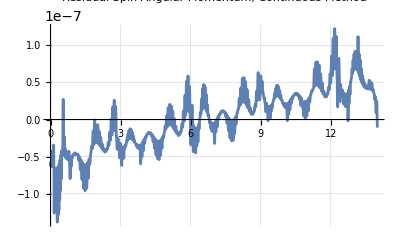

```mathematica
Module[{fϕ,fθ,fψ,X,mean},
fϕ[u_]:=((ϕ[t]/.nsoln[[1]])/.{t->u});
fθ[u_]:=((θ[t]/.nsoln[[1]])/.{t->u});
fψ[u_]:=((ψ[t]/.nsoln[[1]])/.{t->u});
X[u_]:={fϕ[u],fθ[u],fψ[u],fϕ'[u],fθ'[u],fψ'[u]};
mean=Mean[Table[(pψ[X[u]]/.numRules4),{u,0,14,1}]];
Plot[(pψ[X[u]]/.numRules4)-mean,{u,0,14},
PlotLabel->"Residual Spin Angular Momentum, Continuous Method",
FrameLabel->{{"Angular Momentum [Joule-sec]",""},{"Time [sec]",""}},
Frame->Automatic,GridLines->Automatic]]
```

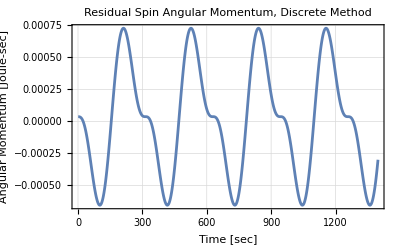

```mathematica
Module[{mean=Mean@Table[pψ[dsoln[[;;,u]]]/.numRules4,{u,3,len}]},
ListLinePlot[Table[(pψ[dsoln[[;;,u]]]/.numRules4)-mean,{u,3,len}],
PlotLabel->"Residual Spin Angular Momentum, Discrete Method",
FrameLabel->{{"Angular Momentum [Joule-sec]",""},{"Time [sec]",""}},
Frame->True,GridLines->Automatic]]
```